## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="G3PD2";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=10;

(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/MASSef/"; (*if using Linux this needs to end with / and the equivalent for macOS and Windows *)
kineticDataFileName =  "kinetic_data.csv";

mainFolder = "fit_G3PD2_typeI";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological, Q10];
```

(glyc3p^c+nadp^c⇌dhap^c+h^c+nadph^c)^G3PD2

ordered bi bi; [nadp,glyc3p,dhap,nadph]

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | glyc3p | nadp | 0.000099 | 0.00009405
0.00010395 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nadph | 3.4×10^-6 | 3.23×10^-6
3.57×10^-6 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | dhap | 0.00018 | 0.000171
0.000189 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | nadp | 0.000165 | 0.00015675
0.00017325 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | glyc3p | 0.00003 | 0.0000285
0.0000315 |  | M | 7.4 | 23 | trishcl | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | glyc3p | 4.2×10^-6 | 3.99×10^-6
4.41×10^-6 | nadph | 0.0001 | Competitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | glyc3p | 6.5×10^-6 | 6.175×10^-6
6.825×10^-6 | dhap | 0.0001 | NonCompetitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | glyc3p | 2.5×10^-6 | 2.375×10^-6
2.625×10^-6 | dhap | 0.0001 | NonCompetitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | nadp | 0.0013 | 0.001235
0.001365 | nadph | 0.00001 | NonCompetitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | nadp | 0.0013 | 0.001235
0.001365 | nadph | 0.00001 | NonCompetitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | nadp | 0.000187 | 0.00017765
0.00019635 | dhap | 0.002 | Competitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | dhap | 0.000038 | 0.0000361
0.0000399 | nadp | 0.002 | Competitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | dhap | 0.00024 | 0.000228
0.000252 | glyc3p | 0.0001 | NonCompetitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | dhap | 0.00012 | 0.000114
0.000126 | glyc3p | 0.0001 | NonCompetitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | nadph | 8.×10^-7 | 7.6×10^-7
8.4×10^-7 | nadp | 0.0001 | NonCompetitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | nadph | 6.×10^-7 | 5.7×10^-7
6.3×10^-7 | nadp | 0.0001 | NonCompetitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | nadph | 4.×10^-7 | 3.8×10^-7
4.2×10^-7 | glyc3p | 0.0002 | Competitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* If a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1,1,1};
s05Priorities = Null;
kcatPriorities = Null;
inhibitionPriorities={1,1,1, 1,1,1,1,1,1,1,1,1};
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(glyc3p^c+nadp^c⇌dhap^c+h^c+nadph^c)^G3PD2

ordered bi bi; [nadp,glyc3p,dhap,nadph]

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | glyc3p | nadp | 0.000099 | 0.00009405
0.00010395 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nadph | 3.4×10^-6 | 3.23×10^-6
3.57×10^-6 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | dhap | 0.00018 | 0.000171
0.000189 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | nadp | 0.000165 | 0.00015675
0.00017325 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | glyc3p | 0.00003 | 0.0000285
0.0000315 |  | M | 7.4 | 23 | trishcl | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | glyc3p | 4.2×10^-6 | 3.99×10^-6
4.41×10^-6 | nadph | 0.0001 | Competitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | glyc3p | 6.5×10^-6 | 6.175×10^-6
6.825×10^-6 | dhap | 0.0001 | NonCompetitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | glyc3p | 2.5×10^-6 | 2.375×10^-6
2.625×10^-6 | dhap | 0.0001 | NonCompetitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | nadp | 0.0013 | 0.001235
0.001365 | nadph | 0.00001 | NonCompetitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | nadp | 0.0013 | 0.001235
0.001365 | nadph | 0.00001 | NonCompetitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | nadp | 0.000187 | 0.00017765
0.00019635 | dhap | 0.002 | Competitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | dhap | 0.000038 | 0.0000361
0.0000399 | nadp | 0.002 | Competitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | dhap | 0.00024 | 0.000228
0.000252 | glyc3p | 0.0001 | NonCompetitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | dhap | 0.00012 | 0.000114
0.000126 | glyc3p | 0.0001 | NonCompetitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | nadph | 8.×10^-7 | 7.6×10^-7
8.4×10^-7 | nadp | 0.0001 | NonCompetitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | nadph | 6.×10^-7 | 5.7×10^-7
6.3×10^-7 | nadp | 0.0001 | NonCompetitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | nadph | 4.×10^-7 | 3.8×10^-7
4.2×10^-7 | glyc3p | 0.0002 | Competitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_G3PD2[c] + nadp[c] <=> E_G3PD2[c]&nadp",
				"E_G3PD2[c]&nadp + glyc3p[c] <=> E_G3PD2[c]&nadp&glyc3p",
				"E_G3PD2[c]&nadp&glyc3p <=> E_G3PD2[c]&nadph&dhap",
				"E_G3PD2[c]&nadph&dhap <=> E_G3PD2[c]&nadph + dhap[c]",
				"E_G3PD2[c]&nadph <=> E_G3PD2[c] + nadph[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites-> 0];
enzymeModel["Reactions"]
```

{((G3PD2^c)_^+nadp^c⇌(G3PD2^c&nadp^c)_^)^G3PD21,((G3PD2^c&nadph^c)_^⇌(G3PD2^c)_^+nadph^c)^G3PD22,((G3PD2^c&nadp^c)_^+glyc3p^c⇌(G3PD2^c&nadp^c&glyc3p^c)_^)^G3PD23,((G3PD2^c&nadph^c&dhap^c)_^⇌(G3PD2^c&nadph^c)_^+dhap^c)^G3PD24,((G3PD2^c&nadp^c&glyc3p^c)_^⇌(G3PD2^c&nadph^c&dhap^c)_^)^G3PD25}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((G3PD2^c)_^+nadp^c⇌(G3PD2^c&nadp^c)_^)^G3PD21,Overscript[(G3PD2^c&nadph^c)_^⇌(G3PD2^c)_^+nadph^c, G3PD22],((G3PD2^c&nadp^c)_^+glyc3p^c⇌(G3PD2^c&nadp^c&glyc3p^c)_^)^G3PD23,Overscript[(G3PD2^c&nadph^c&dhap^c)_^⇌(G3PD2^c&nadph^c)_^+dhap^c, G3PD24],((G3PD2^c&nadp^c&glyc3p^c)_^⇌(G3PD2^c&nadph^c&dhap^c)_^)^G3PD25};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Build enzyme model

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc=1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={{"prod_inhib_dhap", nadph^c->0},{ "prod_inhib_nadph", dhap^c->0}};
otherMetsForwardZeroSub={{"prod_inhib_glyc3p", nadp^c->0},{"prod_inhib_nadp", glyc3p^c->0}};


inhibitionListSubset=inhibitionList[[{2,3,8,9}]];
customRatiosDataList={};

simulateDataFlag="normal";
nSamples=Null;
paramScanList=Null;

numFits=5;
 flagFitType="log_ssd";
```

```mathematica
{fittingData, filteredDataList, bestFitDetails,dataFilePathList,
{enzymeModelLocal, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub,
	allCatalyticReactions,nonCatalyticReactions, absoluteFlux, absoluteRateForward,
absoluteRateReverse, relativeRateForward, relativeRateReverse, 
	otherAbsoluteRatesForward, otherAbsoluteRatesReverse}}=
buildFullEnzymeModel[enzymeModel, rxn, pathMASSef, inputPath, outputPath, dataFileName, inhibitionList,inhibitionList, KeqList, kmList, 
					 s05List, kcatList,inhibitionList, activationList, otherParmsList,inhibitionListSubset,bufferInfo, ionCharge,
					 catalyticReactionsSetsList, otherMetsReverseZeroSub,  otherMetsForwardZeroSub,   customRatiosDataList, MWCFlag,
					simplifyFlag, simplifyMaxTime, nActiveSites, fitLabel, numFits, simulateDataFlag, nSamples, paramScanList,
					assumedSaturatingConc, flagFitType];
```

prod inhib

Generating flux equation...

{((G3PD2^c&nadp^c&glyc3p^c)_^-((G3PD2^c&nadph^c&dhap^c)_^)/K_G3PD25) Volume_c k_G3PD25^⟶}

Volume_c (-(G3PD2^c&nadph^c&dhap^c)_^ k_G3PD25^⟵+(G3PD2^c&nadp^c&glyc3p^c)_^ k_G3PD25^⟶)

Simplifying...

Added inhibition reactions:

{((G3PD2^c&nadph^c)_^+glyc3p^c⇌(G3PD2^c&nadph^c&glyc3p^c)_^)^G3PD2_Kincu_glyc3p_1_nadph,((G3PD2^c)_^+glyc3p^c⇌(G3PD2^c&glyc3p^c)_^)^G3PD2_Kincc_glyc3p_1_nadph,((G3PD2^c&glyc3p^c)_^+nadph^c⇌(G3PD2^c&nadph^c&glyc3p^c)_^)^G3PD2_NC_glyc3p,((G3PD2^c&nadp^c)_^+dhap^c⇌(G3PD2^c&nadp^c&dhap^c)_^)^G3PD2_Kincu_dhap_1_nadp,((G3PD2^c)_^+dhap^c⇌(G3PD2^c&dhap^c)_^)^G3PD2_Kincc_dhap_1_nadp,((G3PD2^c&dhap^c)_^+nadp^c⇌(G3PD2^c&nadp^c&dhap^c)_^)^G3PD2_NC_dhap}

Generating flux equation...

{((G3PD2^c&nadp^c&glyc3p^c)_^-((G3PD2^c&nadph^c&dhap^c)_^)/K_G3PD25) Volume_c k_G3PD25^⟶}

Volume_c (-(G3PD2^c&nadph^c&dhap^c)_^ k_G3PD25^⟵+(G3PD2^c&nadp^c&glyc3p^c)_^ k_G3PD25^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating other relative rate forward equation...

Simplifying...

Generating other relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Configuring enzyme fits...

Running enzyme fit...

5

Evaluating fitness results...

End

## Evaluate fit results

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 0.00477488 | 0.0000227995 | 1.0825×10^-6 | 1.09343 | 0.000099 | 0.0000979175
1 | haldaneRatio_1 | 0.00477488 | 0.0000227995 | 1.0825×10^-6 | 1.09343 | 0.000099 | 0.0000979175
1 | haldaneRatio_1 | 0.00477488 | 0.0000227995 | 1.0825×10^-6 | 1.09343 | 0.000099 | 0.0000979175
1 | haldaneRatio_1 | 0.00477488 | 0.0000227995 | 1.0825×10^-6 | 1.09343 | 0.000099 | 0.0000979175
1 | haldaneRatio_1 | 0.00477488 | 0.0000227995 | 1.0825×10^-6 | 1.09343 | 0.000099 | 0.0000979175
1 | haldaneRatio_1 | 0.00477488 | 0.0000227995 | 1.0825×10^-6 | 1.09343 | 0.000099 | 0.0000979175
1 | haldaneRatio_1 | 0.00477488 | 0.0000227995 | 1.0825×10^-6 | 1.09343 | 0.000099 | 0.0000979175
1 | haldaneRatio_1 | 0.00477488 | 0.0000227995 | 1.0825×10^-6 | 1.09343 | 0.000099 | 0.0000979175
1 | haldaneRatio_1 | 0.00477488 | 0.0000227995 | 1.0825×10^-6 | 1.09343 | 0.000099 | 0.0000979175
1 | haldaneRatio_1 | 0.00477488 | 0.0000227995 | 1.0825×10^-6 | 1.09343 | 0.000099 | 0.0000979175
1 | haldaneRatio_1 | 0.00477488 | 0.0000227995 | 1.0825×10^-6 | 1.09343 | 0.000099 | 0.0000979175
1 | relRateRev_nadph | 0.0495483 | 0.00245503 | 0.00980196 | 10.7822 | 0.0909091 | 0.0811071
1 | relRateRev_nadph | 0.0471776 | 0.00222573 | 0.0140826 | 10.2938 | 0.136807 | 0.122724
1 | relRateRev_nadph | 0.0438526 | 0.00192305 | 0.0192818 | 9.60438 | 0.20076 | 0.181478
1 | relRateRev_nadph | 0.039447 | 0.00155607 | 0.0247238 | 8.68271 | 0.284747 | 0.260023
1 | relRateRev_nadph | 0.0340295 | 0.00115801 | 0.0291558 | 7.53647 | 0.386863 | 0.357707
1 | relRateRev_nadph | 0.0279474 | 0.000781056 | 0.0311622 | 6.23244 | 0.5 | 0.468838
1 | relRateRev_nadph | 0.0217788 | 0.000474318 | 0.0299891 | 4.8911 | 0.613137 | 0.583148
1 | relRateRev_nadph | 0.016135 | 0.000260337 | 0.0260856 | 3.64704 | 0.715253 | 0.689167
1 | relRateRev_nadph | 0.0114374 | 0.000130815 | 0.0207737 | 2.59919 | 0.79924 | 0.778466
1 | relRateRev_nadph | 0.00782604 | 0.0000612469 | 0.0154155 | 1.78587 | 0.863193 | 0.847778
1 | relRateRev_nadph | 0.00521559 | 0.0000272024 | 0.0108523 | 1.19375 | 0.909091 | 0.898239
1 | relRateRev_dhap | 0.0345958 | 0.00119687 | 0.00696086 | 7.65695 | 0.0909091 | 0.0839482
1 | relRateRev_dhap | 0.0329096 | 0.00108304 | 0.00998378 | 7.29771 | 0.136807 | 0.126823
1 | relRateRev_dhap | 0.030549 | 0.000933244 | 0.0136366 | 6.79248 | 0.20076 | 0.187123
1 | relRateRev_dhap | 0.0274295 | 0.000752375 | 0.0174281 | 6.12055 | 0.284747 | 0.267319
1 | relRateRev_dhap | 0.0236061 | 0.000557246 | 0.0204667 | 5.29041 | 0.386863 | 0.366397
1 | relRateRev_dhap | 0.0193304 | 0.000373662 | 0.0217669 | 4.35338 | 0.5 | 0.478233
1 | relRateRev_dhap | 0.0150121 | 0.000225364 | 0.020832 | 3.39761 | 0.613137 | 0.592305
1 | relRateRev_dhap | 0.0110773 | 0.000122707 | 0.0180129 | 2.5184 | 0.715253 | 0.69724
1 | relRateRev_dhap | 0.00781415 | 0.000061061 | 0.0142519 | 1.78319 | 0.79924 | 0.784988
1 | relRateRev_dhap | 0.00531282 | 0.000028226 | 0.0104953 | 1.21587 | 0.863193 | 0.852698
1 | relRateRev_dhap | 0.00350874 | 0.0000123113 | 0.00731512 | 0.804663 | 0.909091 | 0.901776
1 | relRateFor_nadp | 0.0487994 | 0.00238138 | 0.00966198 | 10.6282 | 0.0909091 | 0.0812471
1 | relRateFor_nadp | 0.0464591 | 0.00215844 | 0.0138794 | 10.1453 | 0.136807 | 0.122927
1 | relRateFor_nadp | 0.0431769 | 0.00186424 | 0.0189992 | 9.46363 | 0.20076 | 0.181761
1 | relRateFor_nadp | 0.0388285 | 0.00150766 | 0.0243532 | 8.55258 | 0.284747 | 0.260394
1 | relRateFor_nadp | 0.0334823 | 0.00112106 | 0.0287048 | 7.41988 | 0.386863 | 0.358158
1 | relRateFor_nadp | 0.0274811 | 0.000755212 | 0.0306586 | 6.13171 | 0.5 | 0.469341
1 | relRateFor_nadp | 0.0213959 | 0.000457783 | 0.0294747 | 4.80719 | 0.613137 | 0.583662
1 | relRateFor_nadp | 0.0158292 | 0.000250564 | 0.0256002 | 3.57919 | 0.715253 | 0.689653
1 | relRateFor_nadp | 0.0111967 | 0.000125367 | 0.0203422 | 2.54519 | 0.79924 | 0.778898
1 | relRateFor_nadp | 0.00763583 | 0.0000583058 | 0.0150441 | 1.74285 | 0.863193 | 0.848149
1 | relRateFor_nadp | 0.00506212 | 0.0000256251 | 0.0105348 | 1.15883 | 0.909091 | 0.898556
1 | relRateFor_glyc3p | 1.03755 | 1.07652 | 0.900293 | 990.322 | 0.0909091 | 0.991202
1 | relRateFor_glyc3p | 0.861466 | 0.742125 | 0.857624 | 626.886 | 0.136807 | 0.994431
1 | relRateFor_glyc3p | 0.695791 | 0.484125 | 0.795719 | 396.353 | 0.20076 | 0.996479
1 | relRateFor_glyc3p | 0.544573 | 0.29656 | 0.713028 | 250.407 | 0.284747 | 0.997776
1 | relRateFor_glyc3p | 0.411832 | 0.169606 | 0.611732 | 158.126 | 0.386863 | 0.998595
1 | relRateFor_glyc3p | 0.300645 | 0.0903873 | 0.499114 | 99.8227 | 0.5 | 0.999114
1 | relRateFor_glyc3p | 0.2122 | 0.0450287 | 0.386304 | 63.0045 | 0.613137 | 0.999441
1 | relRateFor_glyc3p | 0.145387 | 0.0211374 | 0.284394 | 39.7614 | 0.715253 | 0.999647
1 | relRateFor_glyc3p | 0.0972262 | 0.00945293 | 0.200538 | 25.091 | 0.79924 | 0.999778
1 | relRateFor_glyc3p | 0.0638312 | 0.00407442 | 0.136667 | 15.8327 | 0.863193 | 0.99986
1 | relRateFor_glyc3p | 0.0413544 | 0.00171018 | 0.0908208 | 9.99029 | 0.909091 | 0.999912
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0318295 | 0.00101312 | 0.0044168 | 7.06688 | 0.0625 | 0.0580832
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0266553 | 0.000710505 | 0.010365 | 5.95305 | 0.174112 | 0.163747
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0159916 | 0.000255731 | 0.0144609 | 3.61523 | 0.4 | 0.385539
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0024881 | 6.19065×10^-6 | 0.00387474 | 0.571269 | 0.678269 | 0.674394
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.00703014 | 0.0000494229 | 0.0141906 | 1.63192 | 0.869565 | 0.883756
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0307994 | 0.000948603 | 0.00326009 | 6.8462 | 0.047619 | 0.044359
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0269559 | 0.000726623 | 0.00821638 | 6.01813 | 0.136527 | 0.128311
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0183256 | 0.000335828 | 0.0137728 | 4.13184 | 0.333333 | 0.319561
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.00578153 | 0.0000334261 | 0.00810083 | 1.32242 | 0.612574 | 0.604473
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.00438468 | 0.0000192254 | 0.00845603 | 1.01472 | 0.833333 | 0.841789
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0302548 | 0.000915353 | 0.00217075 | 6.72931 | 0.0322581 | 0.0300873
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0277751 | 0.000771454 | 0.00590763 | 6.19523 | 0.0953577 | 0.08945
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0216376 | 0.000468188 | 0.0121504 | 4.86017 | 0.25 | 0.23785
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0109921 | 0.000120826 | 0.0128254 | 2.49926 | 0.513167 | 0.500342
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.000389731 | 1.5189×10^-7 | 0.00068999 | 0.0896987 | 0.769231 | 0.768541
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.0243094 | 0.000590946 | 0.00282956 | 5.75706 | 0.0491493 | 0.0519789
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.0219894 | 0.000483533 | 0.00706184 | 5.19362 | 0.135972 | 0.143033
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.0174274 | 0.000303713 | 0.0126131 | 4.0944 | 0.308057 | 0.32067
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.0120401 | 0.000144963 | 0.0144383 | 2.81111 | 0.513614 | 0.528053
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.00847694 | 0.0000718585 | 0.0128311 | 1.97106 | 0.650976 | 0.663808
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.00332888 | 0.0000110815 | 0.000259141 | 0.769449 | 0.0336788 | 0.0339379
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.00402988 | 0.0000162399 | 0.00088391 | 0.932232 | 0.0948165 | 0.0957004
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.00549871 | 0.0000302359 | 0.00283635 | 1.27417 | 0.222603 | 0.225439
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.00740654 | 0.0000548568 | 0.00667267 | 1.72004 | 0.387936 | 0.394609
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.00878589 | 0.0000771919 | 0.0103616 | 2.04363 | 0.50702 | 0.517382
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.0208877 | 0.000436294 | 0.000970501 | 4.69573 | 0.0206677 | 0.0196972
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.0176544 | 0.000311679 | 0.00235281 | 3.98357 | 0.0590629 | 0.0567101
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.0104865 | 0.000109966 | 0.00341563 | 2.38568 | 0.143172 | 0.139756
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.000288593 | 8.32859×10^-8 | 0.000173025 | 0.0664289 | 0.260467 | 0.260294
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.00779819 | 0.0000608117 | 0.00636928 | 1.81182 | 0.351541 | 0.357911
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.0962793 | 0.00926971 | 0.0150416 | 24.8186 | 0.0606061 | 0.0756476
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.0449731 | 0.00202258 | 0.0174754 | 10.9106 | 0.160169 | 0.177644
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.0321919 | 0.00103632 | 0.0238146 | 7.14439 | 0.333333 | 0.309519
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.0986601 | 0.00973382 | 0.102929 | 20.3217 | 0.506498 | 0.403569
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.136092 | 0.018521 | 0.16304 | 26.9015 | 0.606061 | 0.443021
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.178298 | 0.0317902 | 0.0230746 | 50.7641 | 0.0454545 | 0.0685291
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.075078 | 0.0056367 | 0.0226698 | 18.8716 | 0.120127 | 0.142796
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.0613091 | 0.00375881 | 0.0329145 | 13.1658 | 0.25 | 0.217086
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.166179 | 0.0276153 | 0.120778 | 31.7942 | 0.379873 | 0.259096
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.220818 | 0.0487604 | 0.18117 | 39.8574 | 0.454545 | 0.273376
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.279499 | 0.0781198 | 0.0273717 | 90.3265 | 0.030303 | 0.0576747
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.107426 | 0.0115404 | 0.0224746 | 28.0637 | 0.0800844 | 0.102559
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.0885963 | 0.0078493 | 0.0307563 | 18.4538 | 0.166667 | 0.13591
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.224599 | 0.0504446 | 0.102259 | 40.3787 | 0.253249 | 0.15099
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.291682 | 0.0850783 | 0.148218 | 48.9121 | 0.30303 | 0.154812
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.184985 | 0.0342194 | 0.0331897 | 53.1035 | 0.0625 | 0.0956897
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.158361 | 0.0250783 | 0.0766088 | 43.9996 | 0.174112 | 0.250721
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.10901 | 0.0118833 | 0.114127 | 28.5318 | 0.4 | 0.514127
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0550395 | 0.00302935 | 0.0916437 | 13.5114 | 0.678269 | 0.769913
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0214806 | 0.000461414 | 0.0440908 | 5.07044 | 0.869565 | 0.913656
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0683196 | 0.00466756 | 0.00811239 | 17.036 | 0.047619 | 0.0557314
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0614671 | 0.0037782 | 0.0207574 | 15.2039 | 0.136527 | 0.157284
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0466723 | 0.0021783 | 0.037818 | 11.3454 | 0.333333 | 0.371151
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0265095 | 0.000702753 | 0.0385565 | 6.29418 | 0.612574 | 0.651131
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0112065 | 0.000125587 | 0.0217832 | 2.61398 | 0.833333 | 0.855117
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0262126 | 0.0006871 | 0.0018894 | 5.85714 | 0.0322581 | 0.0303687
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0245508 | 0.000602743 | 0.00524107 | 5.49622 | 0.0953577 | 0.0901166
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0204511 | 0.000418248 | 0.0114997 | 4.59989 | 0.25 | 0.2385
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0133841 | 0.000179134 | 0.0155736 | 3.0348 | 0.513167 | 0.497593
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.00639564 | 0.0000409042 | 0.0112451 | 1.46186 | 0.769231 | 0.757986
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.180128 | 0.0324461 | 0.0321255 | 51.4007 | 0.0625 | 0.0946255
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.154454 | 0.0238561 | 0.0743633 | 42.7099 | 0.174112 | 0.248476
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.106697 | 0.0113842 | 0.111395 | 27.8488 | 0.4 | 0.511395
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0542722 | 0.00294547 | 0.0902845 | 13.311 | 0.678269 | 0.768553
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0215838 | 0.000465861 | 0.044308 | 5.09542 | 0.869565 | 0.913873
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.12017 | 0.0144408 | 0.0151797 | 31.8773 | 0.047619 | 0.0627987
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.107603 | 0.0115785 | 0.038386 | 28.116 | 0.136527 | 0.174913
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0809512 | 0.0065531 | 0.0683002 | 20.4901 | 0.333333 | 0.401634
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0457215 | 0.00209045 | 0.0680074 | 11.1019 | 0.612574 | 0.680581
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0197585 | 0.000390399 | 0.0387887 | 4.65465 | 0.833333 | 0.872122
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.073016 | 0.00533133 | 0.00590597 | 18.3085 | 0.0322581 | 0.038164
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0680957 | 0.00463702 | 0.0161876 | 16.9757 | 0.0953577 | 0.111545
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0561114 | 0.00314848 | 0.0344798 | 13.7919 | 0.25 | 0.28448
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0363974 | 0.00132477 | 0.0448612 | 8.74203 | 0.513167 | 0.558028
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0180294 | 0.00032506 | 0.0326062 | 4.2388 | 0.769231 | 0.801837
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.171415 | 0.029383 | 0.0172777 | 32.6116 | 0.0529801 | 0.0357025
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.164873 | 0.0271832 | 0.0457214 | 31.5889 | 0.144739 | 0.0990176
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.152098 | 0.0231338 | 0.0945491 | 29.5466 | 0.32 | 0.225451
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.137155 | 0.0188115 | 0.140429 | 27.0803 | 0.518565 | 0.378136
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.127352 | 0.0162186 | 0.163972 | 25.4156 | 0.645161 | 0.481189
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.0145327 | 0.000211199 | 0.00123025 | 3.29091 | 0.0373832 | 0.0361529
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.0355996 | 0.00126733 | 0.00815078 | 7.87015 | 0.103566 | 0.0954151
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.0747144 | 0.00558224 | 0.0371886 | 15.8051 | 0.235294 | 0.198106
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.117492 | 0.0138044 | 0.0932977 | 23.7029 | 0.393613 | 0.300315
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.14404 | 0.0207474 | 0.141136 | 28.2271 | 0.5 | 0.358864
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.195832 | 0.0383503 | 0.013406 | 56.9757 | 0.0235294 | 0.0369354
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.134241 | 0.0180206 | 0.023909 | 36.22 | 0.0660105 | 0.0899194
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.0292798 | 0.000857305 | 0.0107298 | 6.97438 | 0.153846 | 0.164576
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.0756107 | 0.00571698 | 0.0424412 | 15.9787 | 0.265611 | 0.223169
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.137094 | 0.0187947 | 0.0933449 | 27.07 | 0.344828 | 0.251483
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.290622 | 0.0844611 | 0.0282483 | 48.7872 | 0.0579011 | 0.0296527
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.241605 | 0.0583731 | 0.0662095 | 42.6683 | 0.155173 | 0.0889631
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.14524 | 0.0210947 | 0.0940974 | 28.4253 | 0.331034 | 0.236937
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.0169214 | 0.000286334 | 0.0197161 | 3.82137 | 0.515944 | 0.496228
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.0825536 | 0.00681509 | 0.131188 | 20.9354 | 0.626632 | 0.75782
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.178124 | 0.0317281 | 0.0142915 | 33.6446 | 0.0424779 | 0.0281864
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.126938 | 0.0161133 | 0.0290428 | 25.3445 | 0.114592 | 0.0855493
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.0315077 | 0.000992733 | 0.0173146 | 6.99799 | 0.247423 | 0.230108
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.0959109 | 0.0091989 | 0.0965282 | 24.7128 | 0.390601 | 0.487129
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.196226 | 0.0385048 | 0.273075 | 57.1181 | 0.478088 | 0.751162
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.033614 | 0.0011299 | 0.0020641 | 7.44796 | 0.0277136 | 0.0256495
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.0236589 | 0.000559742 | 0.00421248 | 5.59877 | 0.0752393 | 0.0794518
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.121734 | 0.0148191 | 0.053183 | 32.353 | 0.164384 | 0.217567
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.252253 | 0.0636314 | 0.207021 | 78.7527 | 0.262875 | 0.469896
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.35719 | 0.127585 | 0.413868 | 127.609 | 0.324324 | 0.738192
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.107992 | 0.0116623 | 0.0137597 | 22.0156 | 0.0625 | 0.0487403
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.096444 | 0.00930145 | 0.0346729 | 19.9141 | 0.174112 | 0.139439
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0720887 | 0.00519678 | 0.0611782 | 15.2946 | 0.4 | 0.338822
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0400769 | 0.00160616 | 0.0597899 | 8.81507 | 0.678269 | 0.618479
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0166167 | 0.000276115 | 0.0326423 | 3.75386 | 0.869565 | 0.836923
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.00642266 | 0.0000412505 | 0.000709458 | 1.48986 | 0.047619 | 0.0483285
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.00583216 | 0.0000340141 | 0.00184579 | 1.35196 | 0.136527 | 0.138373
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.00452788 | 0.0000205017 | 0.00349346 | 1.04804 | 0.333333 | 0.336827
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.00268399 | 7.20381×10^-6 | 0.0037975 | 0.619926 | 0.612574 | 0.616372
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.00123179 | 1.51731×10^-6 | 0.00236694 | 0.284033 | 0.833333 | 0.8357
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.168288 | 0.028321 | 0.0152674 | 47.329 | 0.0322581 | 0.0475255
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.155102 | 0.0240565 | 0.0409302 | 42.9228 | 0.0953577 | 0.136288
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.124382 | 0.0154709 | 0.0829065 | 33.1626 | 0.25 | 0.332906
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0766344 | 0.00587283 | 0.0990327 | 19.2983 | 0.513167 | 0.6122
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0347268 | 0.00120595 | 0.0640349 | 8.32454 | 0.769231 | 0.833266

### Simulated Data and Best Fit Data Plot

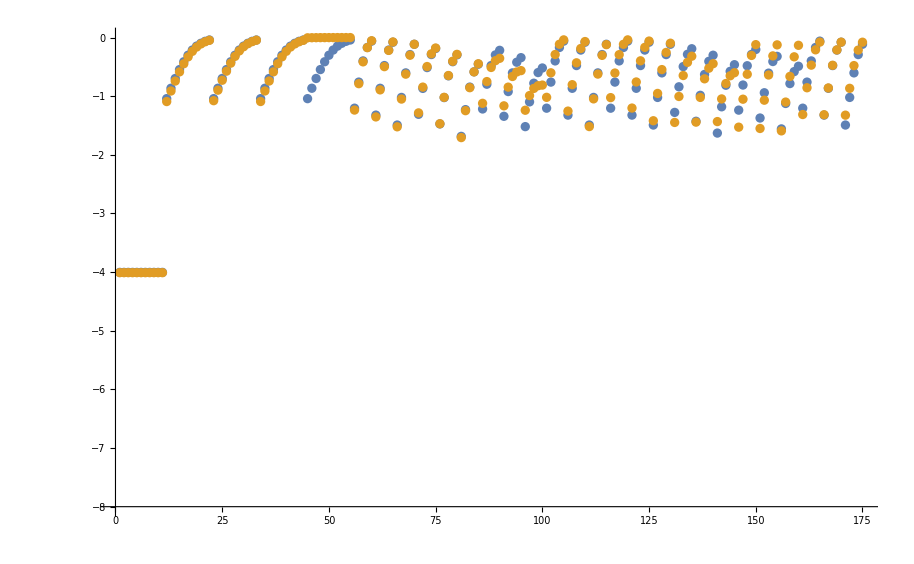

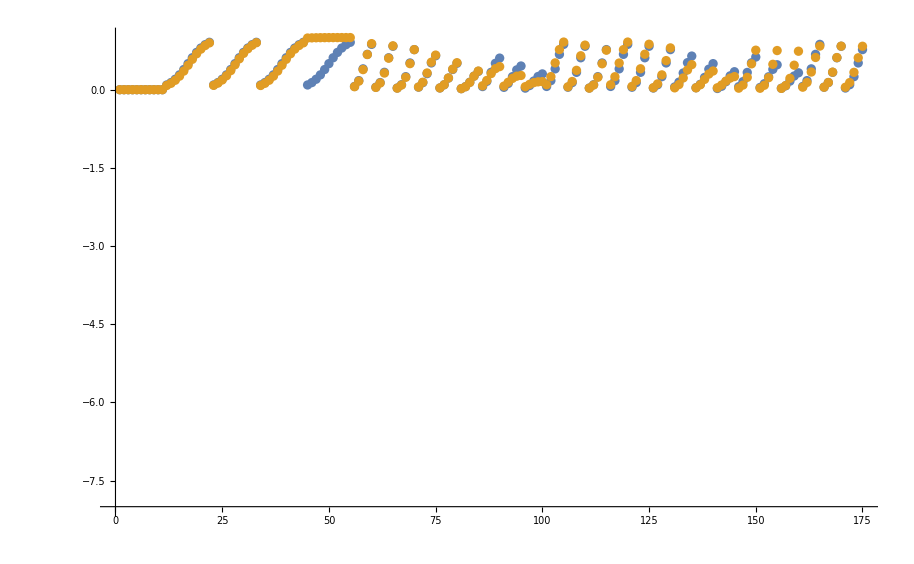

```mathematica
datasetI=1;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

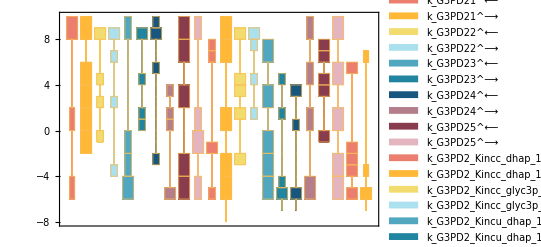

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

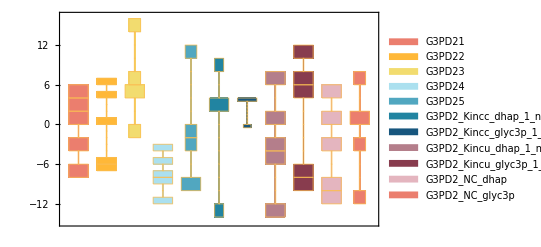

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

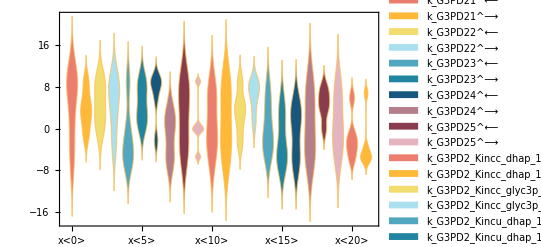

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

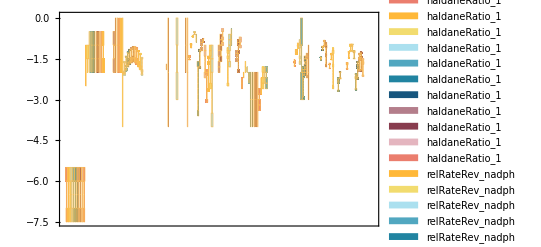

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePathList][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

data value | predicted value | error in %
3.4×10^-6 | 3.85197×10^-6 | 13.2933
0.00018 | 0.000196382 | 9.10122
0.000165 | 0.000186552 | 13.0621
0.00003 | 2.66261×10^-8 | 99.9112

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.000099 | 0.0000979175 | 1.09343

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %
4.2×10^-6 | 4.28999×10^-6 | 2.14254
2.5×10^-6 | 1.67315×10^-6 | 33.0739
0.0013 | 0.473516 | 36324.3
0.000187 | 0.0000244297 | 86.936
0.000038 | 0.0000161746 | 57.4353
0.00012 | 0.0025778 | 2048.17
6.×10^-7 | 6.11105×10^-6 | 918.508
4.×10^-7 | 0.0000221298 | 5432.45

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %
6.5×10^-6 | 6.87333×10^-6 | 5.7436
0.0013 | 0.000349634 | 73.1051
0.00024 | 0.000171345 | 28.6063
8.×10^-7 | 8.38345×10^-6 | 947.931

#### Export rate back calculated parameter error distribution

```mathematica
dataHeader = Import[dataFilePathList][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

FittedModel::varzero: The estimated variance is zero. Properties requiring division by the variance or standard error will not be computed.

-Graphics-